```mathematica
Quit[];
```

```mathematica
DensityMat[k_,χ_,Np_,Nq_]:=Module[{SampleMat,H},
SampleMat=RandomVariate[CircularUnitaryMatrixDistribution[k×χ]];
H=Table[SampleMat[[(i-1)×χ+1;;i×χ,1;;χ]],{i,k}];
Table[Table[Module[{T1,T2},
T1=Fold[Dot,IdentityMatrix[χ],Map[H[[#+1]]&,Join[IntegerDigits[i,k,Np],IntegerDigits[l,k,Nq]]]];
T2=Fold[Dot,IdentityMatrix[χ],Map[H[[#+1]]&,Join[IntegerDigits[j,k,Np],IntegerDigits[l,k,Nq]]]];
Tr[T1]×Conjugate[Tr[T2]]
],{l,k^Nq}]//Total,{i,k^Np},{j,k^Np}]
];
TransferMat[k_,χ_]:=Module[{SampleMat,H},
SampleMat=RandomVariate[CircularUnitaryMatrixDistribution[k×χ]];
H=Table[SampleMat[[(i-1)×χ+1;;i×χ,1;;χ]],{i,k}];
Map[KroneckerProduct[#,Conjugate[#]]&,H]//Total
];
ReducedDensityMat[TMat_,Np_,Nq_]:=Module[{χ,Ep,Eq},
χ=TMat//Length//Sqrt//Round;
Ep=MatrixPower[TMat,Np];Eq=MatrixPower[TMat,Nq];
Table[Total[Table[Ep[[(i-1)×χ+Quotient[k,χ,1]+1]][[(j-1)×χ+Mod[k,χ,1]]]Eq[[(j-1)×χ+Mod[l,χ,1]]][[(i-1)×χ+Quotient[l,χ,1]+1]],{i,χ},{j,χ}],2],{k,χ^2},{l,χ^2}]
];
VonNeumannEntropy[k_,χ_,Np_,Nq_]:=Map[-#×Log[#]&,Eigenvalues[ReducedDensityMat[TransferMat[k,χ],Np,Nq]]]//Total;
(*VonNeumannEntropy[k_,χ_,Np_,Nq_]:=Map[-#×Log[#]&,Eigenvalues[DensityMat[k,χ,Np,Nq]]]//Total;*)
VonNeumannEntropyAvg[k_,χ_,Np_,Nq_]:=ParallelTable[VonNeumannEntropy[k,χ,Np,Nq],{1000}]//Mean;
VonNeumannEntropyAvgList[k_,χ_,Ns_]:=Table[{Np,Re[VonNeumannEntropyAvg[k,χ,Np,Ns-Np]]},{Np,1,Ns/2}];
```

```mathematica
PList=AbsoluteTiming[VonNeumannEntropyAvgList[2,8,50]];
PList[[1]]
```

2295.48

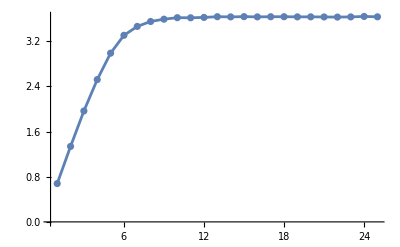

```mathematica
ListPlot[PList[[2]],Joined->True,Mesh->All,PlotRange->All]
```